Project1,Lindstedt method - Hyperbolic case
Pietro De Checchi, Gaia Marangon

__________________
Equations of motion
================

```mathematica
nmax=2;
difx=v
difv=-ω0^2(1+mbk*ε*Cos[u2])(-x+mbk*x^3/6)//Expand(*HYPERB: Sin expanded around (pi,0)*)
```

v

x ω0^2-1/6 mbk x^3 ω0^2+mbk x ε ω0^2 Cos[u2]-1/6 mbk^2 x^3 ε ω0^2 Cos[u2]

____________________________________________________________________
Move to q,p variables (eigenvectors of the linearized equations of motion)
============================================================

```mathematica
xvsolveqp={x->(q+p)/Sqrt[ω0],v->Sqrt[ω0]*(q-p)} (*HYPERB eigenvectors*)
qpsolvexv=Solve[{x==(q+p)/Sqrt[ω0],v==Sqrt[ω0]*(q-p)},{q,p}][[1]]//Expand//Simplify
difq=(q/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp
difp=(p/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp
```

{x→(p+q)/(√ω0),v→(-p+q) √ω0}

{q→(v+x ω0)/(2 √ω0),p→(-v+x ω0)/(2 √ω0)}

-(mbk p^3)/12-1/4 mbk p^2 q-1/4 mbk p q^2-(mbk q^3)/12-1/24 ⅇ^(-ⅈ u2) mbk^2 p^3 ε-1/24 ⅇ^(ⅈ u2) mbk^2 p^3 ε-1/8 ⅇ^(-ⅈ u2) mbk^2 p^2 q ε-1/8 ⅇ^(ⅈ u2) mbk^2 p^2 q ε-1/8 ⅇ^(-ⅈ u2) mbk^2 p q^2 ε-1/8 ⅇ^(ⅈ u2) mbk^2 p q^2 ε-1/24 ⅇ^(-ⅈ u2) mbk^2 q^3 ε-1/24 ⅇ^(ⅈ u2) mbk^2 q^3 ε+q ω0+1/4 ⅇ^(-ⅈ u2) mbk p ε ω0+1/4 ⅇ^(ⅈ u2) mbk p ε ω0+1/4 ⅇ^(-ⅈ u2) mbk q ε ω0+1/4 ⅇ^(ⅈ u2) mbk q ε ω0

(mbk p^3)/12+1/4 mbk p^2 q+1/4 mbk p q^2+(mbk q^3)/12+1/24 ⅇ^(-ⅈ u2) mbk^2 p^3 ε+1/24 ⅇ^(ⅈ u2) mbk^2 p^3 ε+1/8 ⅇ^(-ⅈ u2) mbk^2 p^2 q ε+1/8 ⅇ^(ⅈ u2) mbk^2 p^2 q ε+1/8 ⅇ^(-ⅈ u2) mbk^2 p q^2 ε+1/8 ⅇ^(ⅈ u2) mbk^2 p q^2 ε+1/24 ⅇ^(-ⅈ u2) mbk^2 q^3 ε+1/24 ⅇ^(ⅈ u2) mbk^2 q^3 ε-p ω0-1/4 ⅇ^(-ⅈ u2) mbk p ε ω0-1/4 ⅇ^(ⅈ u2) mbk p ε ω0-1/4 ⅇ^(-ⅈ u2) mbk q ε ω0-1/4 ⅇ^(ⅈ u2) mbk q ε ω0

____________________________________________________________________
Expansion of the equations of motion 
============================================================

```mathematica
repser={q->Sum[mbk^k*q[k],{k,0,nmax}],p->Sum[mbk^k*p[k],{k,0,nmax}]};
difqser=difq/.repser//Expand;
difpser=difp/.repser//Expand;
qdotser=(Sum[Sum[mbk^k ω[k],{k,0,nmax-l}]*(mbk^l*dqu[l]),{l,0,nmax}]+ω*Sum[mbk^k*dqu2[k],{k,0,nmax}]//Expand)/.ω[0]->ω0;
pdotser=(Sum[Sum[mbk^k ω[k],{k,0,nmax-l}]*(mbk^l*dpu[l]),{l,0,nmax}]+ω*Sum[mbk^k*dpu2[k],{k,0,nmax}]//Expand)/.ω[0]->ω0;
eqqser=difqser-qdotser;
eqpser=difpser-pdotser;
```

```mathematica
Coefficient[eqqser,mbk,0]
Coefficient[eqpser,mbk,0]
```

-ω0 dqu[0]-ω dqu2[0]+ω0 q[0]

-ω0 dpu[0]-ω dpu2[0]-ω0 p[0]

____________________________________________________________________
Solution at order 0 
============================================================

```mathematica
solqporder[0]={q[0]->C1*E^(u),p[0]->C2*E^(-u)};
qsol[0]=q[0]/.solqporder[0];
psol[0]=p[0]/.solqporder[0];
solqpallorder[0]=Flatten[{solqporder[0],dqu[0]->D[qsol[0],u],dqu2[0]->D[qsol[0],u2],dpu[0]->D[psol[0],u],dpu2[0]->D[psol[0],u2]}]
```

{q[0]→C1 ⅇ^u,p[0]→C2 ⅇ^-u,dqu[0]→C1 ⅇ^u,dqu2[0]→0,dpu[0]→-C2 ⅇ^-u,dpu2[0]→0}

____________________________________________________________________
Iterative computation of the Lindstedt series at orders 1 to nmax
============================================================

```mathematica
Do[
Print["order ",iord," computing"];
Clear[eqqorder,eqporder,lisexpq,lisexpp,eqqordernew,eqpordernew,eqqordernonsec,eqpordernonsec];
eqqorder=(Coefficient[eqqser,mbk,iord]/.Flatten[Table[solqpallorder[j],{j,0,iord-1}]])/.{q[iord]->0,dqu[iord]->0,dqu2[iord]->0}//Expand;
eqporder=(Coefficient[eqpser,mbk,iord]/.Flatten[Table[solqpallorder[j],{j,0,iord-1}]])/.{p[iord]->0,dpu[iord]->0,dpu2[iord]->0}//Expand;
(*      Print[eqqorder];        *)
lisexpq=Union[Table[E^Exponent[eqqorder[[i]],E],{i,1,Length[eqqorder]}]];
lisexpp=Union[Table[E^Exponent[eqporder[[i]],E],{i,1,Length[eqporder]}]];
eqqordernew=Sum[((Coefficient[eqqorder,lisexpq[[i]]]/.{E^w_->0})//Simplify)*lisexpq[[i]],{i,1,Length[lisexpq]}];
eqpordernew=Sum[((Coefficient[eqporder,lisexpp[[i]]]/.{E^w_->0})//Simplify)*lisexpp[[i]],{i,1,Length[lisexpp]}];
(*           Print[eqqordernew];   *)
solome[iord]=Solve[(Coefficient[eqqordernew,E^(u)]/.E^w_->0)==0,ω[iord]][[1]]//Simplify//Expand; (*HYPERB eigenvectors*)
eqqordernonsec=eqqordernew/.{E^(u)->0}; (*HYPERB eigenvectors*)
eqpordernonsec=eqpordernew/.{E^(-u)->0}; (*HYPERB eigenvectors*)
qsol[iord]=Sum[(eqqordernonsec[[i]]/((Exponent[eqqordernonsec[[i]],E]/.{u->ω0,u2->ω})-ω0))/.{E^w_->E^ExpandAll[w]},{i,1,Length[eqqordernonsec]}]//ExpToTrig//Simplify//TrigToExp//Expand;(*HYPERB eigenvalues*)
psol[iord]=Sum[eqpordernonsec[[i]]/((Exponent[eqpordernonsec[[i]],E]/.{u->ω0,u2->ω})+ω0),{i,1,Length[eqpordernonsec]}]//ExpToTrig//Simplify//TrigToExp//Expand; (*HYPERB eigenvalues*)
solqpallorder[iord]=Flatten[{q[iord]->qsol[iord],p[iord]->psol[iord],dqu[iord]->D[qsol[iord],u],dqu2[iord]->D[qsol[iord],u2],dpu[iord]->D[psol[iord],u],dpu2[iord]->D[psol[iord],u2],solome[iord]}];
Print["order ",iord," computed"],
{iord,1,nmax}];
```

order 1 computing

order 1 computed

order 2 computing

order 2 computed

```mathematica
solqpallorder[0]
solqpallorder[1]
solqpallorder[2]
```

{q[0]→C1 ⅇ^u,p[0]→C2 ⅇ^-u,dqu[0]→C1 ⅇ^u,dqu2[0]→0,dpu[0]→-C2 ⅇ^-u,dpu2[0]→0}

{q[1]→(C2^3 ⅇ^(-3 u) ω^2)/(48 ω0 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^-u ω^2)/(8 ω0 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω^2)/(24 ω0 (ω^2+4 ω0^2))+(C2^3 ⅇ^(-3 u) ω0)/(12 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^-u ω0)/(2 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω0)/(6 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(C2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),p[1]→-(C2^3 ⅇ^(-3 u) ω^2)/(24 ω0 (ω^2+4 ω0^2))+(C1^2 C2 ⅇ^u ω^2)/(8 ω0 (ω^2+4 ω0^2))+(C1^3 ⅇ^(3 u) ω^2)/(48 ω0 (ω^2+4 ω0^2))-(C2^3 ⅇ^(-3 u) ω0)/(6 (ω^2+4 ω0^2))+(C1^2 C2 ⅇ^u ω0)/(2 (ω^2+4 ω0^2))+(C1^3 ⅇ^(3 u) ω0)/(12 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C1 ⅇ^(u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(C1 ⅇ^(u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),dqu[1]→-(C2^3 ⅇ^(-3 u) ω^2)/(16 ω0 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^-u ω^2)/(8 ω0 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω^2)/(8 ω0 (ω^2+4 ω0^2))-(C2^3 ⅇ^(-3 u) ω0)/(4 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^-u ω0)/(2 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω0)/(2 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(C2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(C2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),dqu2[1]→(C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(C1 ⅇ^(u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))+(C1 ⅇ^(u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),dpu[1]→(C2^3 ⅇ^(-3 u) ω^2)/(8 ω0 (ω^2+4 ω0^2))+(C1^2 C2 ⅇ^u ω^2)/(8 ω0 (ω^2+4 ω0^2))+(C1^3 ⅇ^(3 u) ω^2)/(16 ω0 (ω^2+4 ω0^2))+(C2^3 ⅇ^(-3 u) ω0)/(2 (ω^2+4 ω0^2))+(C1^2 C2 ⅇ^u ω0)/(2 (ω^2+4 ω0^2))+(C1^3 ⅇ^(3 u) ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C1 ⅇ^(u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(C1 ⅇ^(u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),dpu2[1]→-(C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(C2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))-(C2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2)),ω[1]→-(C1 C2)/4}

{q[2]→(3 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)-(3 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))-(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)+(3 ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(3 ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(C2^5 ⅇ^(-5 u))/(1152 ω0^2)+(7 C1 C2^4 ⅇ^(-3 u))/(768 ω0^2)-(5 C1^4 C2 ⅇ^(3 u))/(192 ω0^2)+(C1^5 ⅇ^(5 u))/(768 ω0^2)+(3 C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)+(3 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))+(3 C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)+(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)+(C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))+(ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)-(ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(ⅈ C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω-2 ⅈ ω0))-(ⅈ C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω-ⅈ ω0) (ω-2 ⅈ ω0))-(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(ⅈ C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω+2 ⅈ ω0))+(ⅈ C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))-(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(23 C1^2 C2^3 ⅇ^-u)/(96 (ω^2+4 ω0^2))-(3 ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(3 ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(23 C1^2 C2^3 ⅇ^-u ω^2)/(384 ω0^2 (ω^2+4 ω0^2))-(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))+(C2 ⅇ^-u ε^2 ω0^2)/(8 (ω^2+4 ω0^2)),p[2]→(3 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)-(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)+(3 ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(3 ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(C2^5 ⅇ^(-5 u))/(768 ω0^2)-(5 C1 C2^4 ⅇ^(-3 u))/(192 ω0^2)+(7 C1^4 C2 ⅇ^(3 u))/(768 ω0^2)-(C1^5 ⅇ^(5 u))/(1152 ω0^2)+(3 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)+(3 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)+(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)+(ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)-(ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(ⅈ C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω-2 ⅈ ω0))-(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(ⅈ C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω+2 ⅈ ω0))+(ⅈ C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))-(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(ⅈ C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(16 ω (ⅈ ω+ω0) (ⅈ ω+2 ω0))+(3 C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))-(3 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))-(C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))+(23 C1^3 C2^2 ⅇ^u)/(96 (ω^2+4 ω0^2))+(3 ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))-(3 ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(23 C1^3 C2^2 ⅇ^u ω^2)/(384 ω0^2 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))+(C1 ⅇ^u ε^2 ω0^2)/(8 (ω^2+4 ω0^2)),dqu[2]→(9 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)+(9 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))-(9 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)-(3 ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(3 ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(9 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(5 C2^5 ⅇ^(-5 u))/(1152 ω0^2)-(7 C1 C2^4 ⅇ^(-3 u))/(256 ω0^2)-(5 C1^4 C2 ⅇ^(3 u))/(64 ω0^2)+(5 C1^5 ⅇ^(5 u))/(768 ω0^2)+(9 C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)-(9 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))+(9 C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)-(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(9 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(3 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)-(3 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))+(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)+(ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(ⅈ C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω-2 ⅈ ω0))+(ⅈ C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω-ⅈ ω0) (ω-2 ⅈ ω0))+(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(ⅈ C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω+2 ⅈ ω0))-(ⅈ C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))+(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(23 C1^2 C2^3 ⅇ^-u)/(96 (ω^2+4 ω0^2))-(3 ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(3 ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))-(23 C1^2 C2^3 ⅇ^-u ω^2)/(384 ω0^2 (ω^2+4 ω0^2))-(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(C2 ⅇ^-u ε^2 ω0^2)/(8 (ω^2+4 ω0^2)),dqu2[2]→-(3 C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)+(3 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))-(3 C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)-(3 C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(3 C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(3 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)+(3 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))-(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)+(ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)-(ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (-ⅈ ω-4 ω0) (ω-2 ⅈ ω0))+(C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)+(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(8 ω^2 (ω-2 ⅈ ω0))-(C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(8 ω (ω-ⅈ ω0) (ω-2 ⅈ ω0))-(ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(8 ω^2 (ω+2 ⅈ ω0))-(C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(8 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))+(ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 C1^2 C2 ⅇ^(u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))-(3 C1^2 C2 ⅇ^(u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2)),dpu[2]→-(9 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)+(9 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)+(3 ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(3 ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(9 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(5 C2^5 ⅇ^(-5 u))/(768 ω0^2)+(5 C1 C2^4 ⅇ^(-3 u))/(64 ω0^2)+(7 C1^4 C2 ⅇ^(3 u))/(256 ω0^2)-(5 C1^5 ⅇ^(5 u))/(1152 ω0^2)-(9 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)-(9 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)+(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(9 C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(3 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)-(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)-(ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(ⅈ C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω-2 ⅈ ω0))-(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(ⅈ C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(16 ω^2 (ω+2 ⅈ ω0))+(ⅈ C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(16 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))-(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(ⅈ C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(16 ω (ⅈ ω+ω0) (ⅈ ω+2 ω0))+(9 C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))-(9 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))-(3 C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))+(23 C1^3 C2^2 ⅇ^u)/(96 (ω^2+4 ω0^2))-(3 ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(3 ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(23 C1^3 C2^2 ⅇ^u ω^2)/(384 ω0^2 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))+(C1 ⅇ^u ε^2 ω0^2)/(8 (ω^2+4 ω0^2)),dpu2[2]→(3 C2^3 ⅇ^(-3 u-ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0)^2)+(3 C2^3 ⅇ^(-3 u+ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0)^2)+(3 C1^2 C2 ⅇ^(u-ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(3 C1^2 C2 ⅇ^(u+ⅈ u2) ε ω^2)/(32 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(3 C1^3 ⅇ^(3 u-ⅈ u2) ε ω)/(64 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(3 ⅈ C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0)^2)+(3 ⅈ C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0)^2)-(ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω ω0)/(16 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))+(3 ⅈ C1^3 ⅇ^(3 u-ⅈ u2) ε ω0)/(32 (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))-(C2^3 ⅇ^(-3 u-ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0)^2)-(C2^3 ⅇ^(-3 u+ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0)^2)-(C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)-(C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^2)/(8 (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(C1^3 ⅇ^(3 u-ⅈ u2) ε ω0^2)/(8 ω (ω+2 ⅈ ω0) (ω+4 ⅈ ω0))+(C2 ⅇ^(-u-2 ⅈ u2) ε^2 ω0^3)/(8 ω^2 (ω-2 ⅈ ω0))+(ⅈ C1^2 C2 ⅇ^(u-ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0) (ω+2 ⅈ ω0)^2)+(C2 ⅇ^(-u+2 ⅈ u2) ε^2 ω0^3)/(8 ω^2 (ω+2 ⅈ ω0))+(C1 ⅇ^(u-2 ⅈ u2) ε^2 ω0^3)/(8 ω (ω+ⅈ ω0) (ω+2 ⅈ ω0))-(ⅈ C1^2 C2 ⅇ^(u+ⅈ u2) ε ω0^3)/(4 ω (ω-2 ⅈ ω0)^2 (ω+2 ⅈ ω0))-(C1 ⅇ^(u+2 ⅈ u2) ε^2 ω0^3)/(8 ω (ⅈ ω+ω0) (ⅈ ω+2 ω0))+(3 ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω)/(64 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))+(3 C1^3 ⅇ^(3 u+ⅈ u2) ε ω0)/(32 (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))-(ⅈ C1^3 ⅇ^(3 u+ⅈ u2) ε ω0^2)/(8 ω (ω-2 ⅈ ω0) (ⅈ ω+4 ω0))+(3 C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(3 C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω)/(32 (ω^2+4 ω0^2))+(ⅈ C1 C2^2 ⅇ^(-u-ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2))-(ⅈ C1 C2^2 ⅇ^(-u+ⅈ u2) ε ω0)/(16 (ω^2+4 ω0^2)),ω[2]→-(17 C1^2 C2^2)/(192 ω0)-(ε^2 ω0^3)/(4 (ω^2+4 ω0^2))}

```mathematica
ω0
ω[1]/.solqpallorder[1]
ω[2]/.solqpallorder[2]
```

ω0

-(C1 C2)/4

-(17 C1^2 C2^2)/(192 ω0)-(ε^2 ω0^3)/(4 (ω^2+4 ω0^2))

____________________________________________________________________
Compose complete solutions, taking care of initial conditions
============================================================

```mathematica
Do[
completeqSol[ordSol] = (q[0]/.solqpallorder[0])+Sum[(q[iord]/.solqpallorder[iord])- (q[iord]/.solqpallorder[iord]/.{u->0,u2->0} )*Exp[ u]  ,{iord,1,ordSol}] //Expand;(*HYPERB eigenvectors*)
completepSol[ordSol] = (p[0]/.solqpallorder[0])+Sum[(p[iord]/.solqpallorder[iord])- (p[iord]/.solqpallorder[iord]/.{u->0,u2->0}) *Exp[- u],{iord,1,ordSol}] //Expand;(*HYPERB eigenvectors*)
completeoSol[ordSol] = ω0 + Sum[ω[iord]/.solqpallorder[iord],{iord,1,ordSol}]  //Expand;
,{ordSol,0,nmax}] ;
```

```mathematica
completeoSol[0]
completeoSol[1]
completeqSol[0] 
completeqSol[1]
completepSol[1];
completepSol[0];
```

ω0

-(C1 C2)/4+ω0

C1 ⅇ^u

C1 ⅇ^u+(C2^3 ⅇ^(-3 u) ω^2)/(48 ω0 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^-u ω^2)/(8 ω0 (ω^2+4 ω0^2))+(C1^3 ⅇ^u ω^2)/(24 ω0 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^u ω^2)/(8 ω0 (ω^2+4 ω0^2))-(C2^3 ⅇ^u ω^2)/(48 ω0 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω^2)/(24 ω0 (ω^2+4 ω0^2))+(C2^3 ⅇ^(-3 u) ω0)/(12 (ω^2+4 ω0^2))+(C1 C2^2 ⅇ^-u ω0)/(2 (ω^2+4 ω0^2))+(C1^3 ⅇ^u ω0)/(6 (ω^2+4 ω0^2))-(C1 C2^2 ⅇ^u ω0)/(2 (ω^2+4 ω0^2))-(C2^3 ⅇ^u ω0)/(12 (ω^2+4 ω0^2))-(C1^3 ⅇ^(3 u) ω0)/(6 (ω^2+4 ω0^2))+(ⅈ C2 ⅇ^(-u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C2 ⅇ^(-u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω ω0)/(4 (ω^2+4 ω0^2))+(C2 ⅇ^u ε ω0^2)/(ω^2+4 ω0^2)-(C2 ⅇ^(-u-ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))-(C2 ⅇ^(-u+ⅈ u2) ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅈ C1 ⅇ^(u-ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))-(ⅈ C1 ⅇ^(u+ⅈ u2) ε ω0^3)/(ω (ω^2+4 ω0^2))

____________________________________________________________________
Go back to original x,v variables 
============================================================

```mathematica
(*INITIAL CONDITIONS*)
C1 = q /. qpsolvexv /. {x->x0,v->v0}
C2 = p /. qpsolvexv /. {x->x0,v->v0}
```

(v0+x0 ω0)/(2 √ω0)

(-v0+x0 ω0)/(2 √ω0)

```mathematica
(*COMPLETE SOLUTION*)
Do[
completexSol[ordSol] = x/.xvsolveqp /.{q->completeqSol[ordSol],p->completepSol[ordSol]}/.qpsolvexv//Expand;
completevSol[ordSol] =v/.xvsolveqp /.{q->completeqSol[ordSol],p->completepSol[ordSol]}/.qpsolvexv//Expand;
,{ordSol,0,nmax}];
```

```mathematica
completexSol[0]
completexSol[1]
completevSol[0]
completevSol[1]
```

(ⅇ^-u x0)/2+(ⅇ^u x0)/2-(ⅇ^-u v0)/(2 ω0)+(ⅇ^u v0)/(2 ω0)

(ⅇ^-u x0)/2+(ⅇ^u x0)/2-(ⅇ^-u v0)/(2 ω0)+(ⅇ^u v0)/(2 ω0)-(ⅇ^(-3 u) v0^2 x0)/(32 (ω^2+4 ω0^2))+(ⅇ^-u v0^2 x0)/(32 (ω^2+4 ω0^2))+(ⅇ^u v0^2 x0)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^2 x0)/(32 (ω^2+4 ω0^2))-(ⅇ^(-3 u) x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^-u x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^u x0^3 ω^2)/(384 (ω^2+4 ω0^2))-(ⅇ^(3 u) x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^(-3 u) v0^3 ω^2)/(384 ω0^3 (ω^2+4 ω0^2))+(3 ⅇ^-u v0^3 ω^2)/(128 ω0^3 (ω^2+4 ω0^2))-(3 ⅇ^u v0^3 ω^2)/(128 ω0^3 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^3 ω^2)/(384 ω0^3 (ω^2+4 ω0^2))-(ⅇ^(-3 u) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^-u v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^u v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(-3 u) v0^3)/(96 ω0 (ω^2+4 ω0^2))+(3 ⅇ^-u v0^3)/(32 ω0 (ω^2+4 ω0^2))-(3 ⅇ^u v0^3)/(32 ω0 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^3)/(96 ω0 (ω^2+4 ω0^2))+(ⅇ^(-3 u) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(7 ⅇ^-u v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(7 ⅇ^u v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(ⅇ^(-3 u) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))-(7 ⅇ^-u v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))+(7 ⅇ^u v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))+(ⅇ^-u v0 ε ω0)/(2 (ω^2+4 ω0^2))-(ⅇ^u v0 ε ω0)/(2 (ω^2+4 ω0^2))+(ⅇ^(-u-ⅈ u2) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(u-ⅈ u2) v0 ε ω0)/(4 (ω^2+4 ω0^2))+(ⅇ^(-u+ⅈ u2) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(u+ⅈ u2) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(-3 u) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^-u x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^u x0^3 ω0^2)/(96 (ω^2+4 ω0^2))-(ⅇ^(3 u) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^-u x0 ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅇ^u x0 ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅇ^(-u-ⅈ u2) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(u-ⅈ u2) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(-u+ⅈ u2) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(u+ⅈ u2) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u-ⅈ u2) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u+ⅈ u2) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u-ⅈ u2) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u+ⅈ u2) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))

(ⅇ^-u v0)/2+(ⅇ^u v0)/2-1/2 ⅇ^-u x0 ω0+1/2 ⅇ^u x0 ω0

(ⅇ^-u v0)/2+(ⅇ^u v0)/2-1/2 ⅇ^-u x0 ω0+1/2 ⅇ^u x0 ω0-(ⅇ^(-3 u) v0^3)/(32 (ω^2+4 ω0^2))+(ⅇ^-u v0^3)/(32 (ω^2+4 ω0^2))+(ⅇ^u v0^3)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^3)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(-3 u) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))+(3 ⅇ^-u v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))+(3 ⅇ^u v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))-(3 ⅇ^(3 u) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))-(ⅇ^(-3 u) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^-u v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^u v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))-(ⅇ^(3 u) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(3 ⅇ^(-3 u) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(5 ⅇ^-u v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(5 ⅇ^u v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(3 ⅇ^(3 u) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(3 ⅇ^(-3 u) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(5 ⅇ^-u v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))+(5 ⅇ^u v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(3 u) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u-ⅈ u2) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u+ⅈ u2) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅇ^(-3 u) x0^3 ω^2 ω0)/(128 (ω^2+4 ω0^2))+(11 ⅇ^-u x0^3 ω^2 ω0)/(384 (ω^2+4 ω0^2))-(11 ⅇ^u x0^3 ω^2 ω0)/(384 (ω^2+4 ω0^2))-(ⅇ^(3 u) x0^3 ω^2 ω0)/(128 (ω^2+4 ω0^2))-(3 ⅇ^(-3 u) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))+(3 ⅇ^-u v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))+(3 ⅇ^u v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(3 u) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))-(ⅇ^-u v0 ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅇ^u v0 ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅇ^(-u-ⅈ u2) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(u-ⅈ u2) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(-u+ⅈ u2) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(u+ⅈ u2) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u-ⅈ u2) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u+ⅈ u2) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(-3 u) x0^3 ω0^3)/(32 (ω^2+4 ω0^2))+(11 ⅇ^-u x0^3 ω0^3)/(96 (ω^2+4 ω0^2))-(11 ⅇ^u x0^3 ω0^3)/(96 (ω^2+4 ω0^2))-(ⅇ^(3 u) x0^3 ω0^3)/(32 (ω^2+4 ω0^2))-(ⅇ^-u x0 ε ω0^3)/(2 (ω^2+4 ω0^2))+(ⅇ^u x0 ε ω0^3)/(2 (ω^2+4 ω0^2))-(ⅇ^(-u-ⅈ u2) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))+(ⅇ^(u-ⅈ u2) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))-(ⅇ^(-u+ⅈ u2) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))+(ⅇ^(u+ⅈ u2) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u-ⅈ u2) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u+ⅈ u2) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-u-ⅈ u2) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(u-ⅈ u2) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(-u+ⅈ u2) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(u+ⅈ u2) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))

____________________________________________________________________
Go back to time variable t 
============================================================

```mathematica
Do[
completexSol[ordSol] = completexSol[ordSol]/.{u->completeoSol[ordSol] t, u2->ω t} //Expand;
completevSol[ordSol] = completevSol[ordSol]/.{u->completeoSol[ordSol] t, u2->ω t} //Expand;
,{ordSol,0,nmax}];
```

```mathematica
completexSol[0]
completexSol[1]
completevSol[0]
completevSol[1]
```

1/2 ⅇ^(-t ω0) x0+1/2 ⅇ^(t ω0) x0-(ⅇ^(-t ω0) v0)/(2 ω0)+(ⅇ^(t ω0) v0)/(2 ω0)

1/2 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0+1/2 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0-(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0)/(2 ω0)+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0)/(2 ω0)-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0)/(32 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0)/(32 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0)/(32 (ω^2+4 ω0^2))-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2)/(384 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2)/(384 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(384 ω0^3 (ω^2+4 ω0^2))+(3 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^3 (ω^2+4 ω0^2))-(3 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^3 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(384 ω0^3 (ω^2+4 ω0^2))-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(96 ω0 (ω^2+4 ω0^2))+(3 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 ω0 (ω^2+4 ω0^2))-(3 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 ω0 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(96 ω0 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(7 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(7 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))-(7 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))+(7 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0)/(32 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(2 (ω^2+4 ω0^2))-(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(2 (ω^2+4 ω0^2))+(ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(4 (ω^2+4 ω0^2))+(ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0)/(4 (ω^2+4 ω0^2))-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^2)/(96 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))-(ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))

1/2 ⅇ^(-t ω0) v0+1/2 ⅇ^(t ω0) v0-1/2 ⅇ^(-t ω0) x0 ω0+1/2 ⅇ^(t ω0) x0 ω0

1/2 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0+1/2 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0-1/2 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ω0+1/2 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ω0-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))+(3 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))+(3 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))-(3 ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω^2)/(128 (ω^2+4 ω0^2))-(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^3 ω^2)/(128 ω0^2 (ω^2+4 ω0^2))+(3 ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(5 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(5 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))-(3 ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω^2)/(128 ω0 (ω^2+4 ω0^2))+(3 ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(5 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))+(5 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0^2 x0 ω0)/(32 (ω^2+4 ω0^2))-(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω ω0)/(4 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2 ω0)/(128 (ω^2+4 ω0^2))+(11 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2 ω0)/(384 (ω^2+4 ω0^2))-(11 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2 ω0)/(384 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω^2 ω0)/(128 (ω^2+4 ω0^2))-(3 ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))+(3 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))+(3 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))-(3 ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 x0^2 ω0^2)/(32 (ω^2+4 ω0^2))-(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 (ω^2+4 ω0^2))-(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(2 (ω^2+4 ω0^2))+(ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω ω0^2)/(4 (ω^2+4 ω0^2))+(ⅇ^(-3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^3)/(32 (ω^2+4 ω0^2))+(11 ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^3)/(96 (ω^2+4 ω0^2))-(11 ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^3)/(96 (ω^2+4 ω0^2))-(ⅇ^(3 t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0^3 ω0^3)/(32 (ω^2+4 ω0^2))-(ⅇ^(-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 (ω^2+4 ω0^2))+(ⅇ^(t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(2 (ω^2+4 ω0^2))-(ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))-(ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))+(ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))+(ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^3)/(4 (ω^2+4 ω0^2))-(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) v0 ε ω0^3)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω-t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))+(ⅈ ⅇ^(-ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))-(ⅈ ⅇ^(ⅈ t ω+t (ω0-((-v0+x0 ω0) (v0+x0 ω0))/(16 ω0))) x0 ε ω0^4)/(2 ω (ω^2+4 ω0^2))

____________________________________________________________________
Comparison with numerical solution
============================================================

```mathematica
(*NUMERICAL PARAMETERS*)
repnum = {ω0 -> 1.0,ω -> 1.1,ε -> 0.1,x0 -> Pi+0.1,v0 -> 0.0};
```

```mathematica
(*NUMERICAL SOLUTION*)
num rhs x = difx/.{u2->ω t, mbk->1.}  /.{x->x[t], v->v[t]} /. repnum;
num rhs v = difv /.{u2->ω t, mbk->1.}  /.{x->x[t], v->v[t]} /. repnum;
numSol substitutionRule = NDSolve[{ x'[t]==num rhs x ,
	    v'[t]==num rhs v , 
	     x[0]== x0 /. repnum,
	     v[0]==v0 /. repnum},
	{x,v},{t,0,1000}][[1]];
{numSol x[t_],numSol v[t_]}={x[t],v[t]}/. numSol substitutionRule;
```

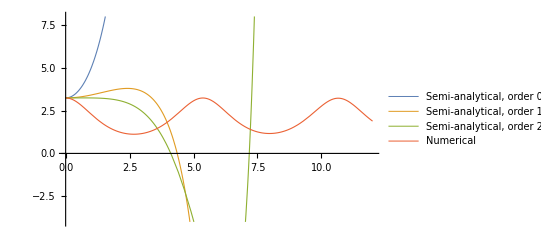

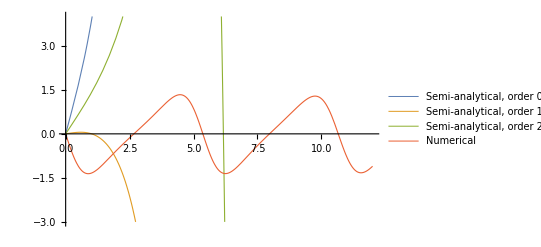

```mathematica
(*COMPARISON: PLOTTING FUNCTIONS*)
nOrder plot=nmax;
listOfFunctions x = Flatten[{Table[completexSol[upToOrder] /. repnum,{upToOrder,0,nOrder plot}],numSol x[t]}];
listOfFunctions v = Flatten[{Table[completevSol[upToOrder] /. repnum,{upToOrder,0,nOrder plot}],numSol v[t]}];
listOfLabels = Flatten[{Table["Semi-analytical, order " <>ToString[upToOrder],{upToOrder,0,nOrder plot}],"Numerical"}];
Plot[listOfFunctions x,{t,0,12},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002],PlotRange->{-4,8}]
Plot[listOfFunctions v,{t,0,12},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002],PlotRange->{-3,4}]
```

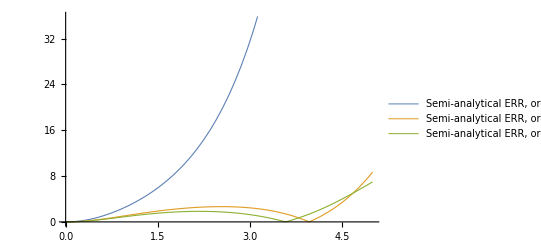

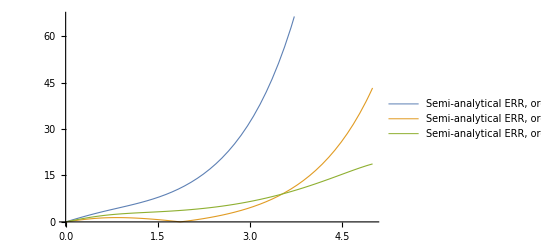

```mathematica
(*COMPARISON: PLOTTING ABSOLUTE ERRORS*)
snOrder plot=nmax;
listOfFunctions x = Flatten[Table[Abs[(completexSol[upToOrder] /. repnum)-numSol x[t]],{upToOrder,0,nOrder plot}]];
listOfFunctions v = Flatten[Table[Abs[(completevSol[upToOrder] /. repnum)-numSol v[t]],{upToOrder,0,nOrder plot}]];
listOfLabels = Flatten[Table["Semi-analytical ERR, order " <>ToString[upToOrder],{upToOrder,0,nOrder plot}]];
Plot[listOfFunctions x,{t,0,5},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
Plot[listOfFunctions v,{t,0,5},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
```